```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### cluster data, vary E20

```mathematica
thisData=Import["data_mechanism3//stabilityPlot_mechanism3_varyE20_kappa_0.25_8.29.23.mx"];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
thisParamSet=Import["data_mechanism3//stabilityPlot_mechanism3_varyE20_kappa_0.25_8.29.23_params.mx"];
```

```mathematica
ss1={};
ss3={};
```

```mathematica
For[i=1,i<=Length[thisData],i++,

For[j=1,j<=Length[thisData[[i]]],j++,

thisCoord={thisData[[i,j,1]],thisData[[i,j,2]]};
(*check that there's an actual solution*)
If[Length[thisData[i,j,3,1]]>1,
If[Length[thisData[[i,j,3]]]==1,AppendTo[ss1,thisCoord],AppendTo[ss3,thisCoord]];
];
]
]
```

```mathematica
(*Export["stabilityPhaseDiagram_mechanism1_varyE20.png",%,ImageResolution->200]*)
```

```mathematica
ss1Height=Table[{ss1[[i,1]],ss1[[i,2]],-10},{i,Length[ss1]}];
```

```mathematica
ss3Height=Table[{ss3[[i,1]],ss3[[i,2]],10},{i,Length[ss3]}];
```

```mathematica
allPoints=Join[ss1Height,ss3Height];
```

```mathematica
(*convert allPoints to matrix format*)
```

```mathematica
xList=DeleteDuplicates[allPoints[[;;,1]]]//Sort;
yList=DeleteDuplicates[allPoints[[;;,2]]]//ReverseSort;
```

```mathematica
plottingMatrix=ConstantArray[0,{Length[yList],Length[xList]}];
```

```mathematica
For[i=1,i<=Length[allPoints],i++,

thisPoint=allPoints[[i]];

rowIndex=Position[yList,thisPoint[[2]]][[1,1]];
colIndex=Position[xList,thisPoint[[1]]][[1,1]];

plottingMatrix[[rowIndex,colIndex]]=thisPoint[[3]];
]
```

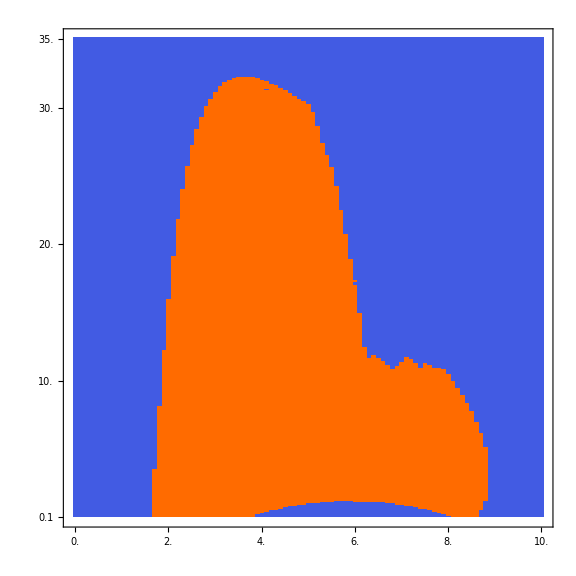

```mathematica
MatrixPlot[plottingMatrix,AspectRatio->1,Frame->{True,True,False,False},LabelStyle->Directive[Black,30],DataRange->{{xList[[1]],xList[[-1]]},{yList[[-1]],yList[[1]]}},ImageSize->Large]
```

```mathematica
Export["interference_mechanism3_phaseDiagram.png",%,ImageResolution->200]
```

interference_mechanism3_phaseDiagram.png